```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 18 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[q1]
q1 = { x[t], y[t], z[t] } 
q1[[1]]
q1[[2]]
```

{x[t],y[t],z[t]}

x[t]

y[t]

```mathematica
D[q1, t]
```

{x'[t],y'[t],z'[t]}

```mathematica
D[q1, t] . D[q1, t]
```

x'[t]^2+y'[t]^2+z'[t]^2

```mathematica
Clear[q2]
q2 = { r[t], θ[t], ϕ[t] }
```

{r[t],θ[t],ϕ[t]}

```mathematica
Clear[r2]  
r2 = { r[t] Cos[ϕ[t]]  Sin[θ[t] ] ,  r[t] Sin[ϕ[t]]  Sin[θ[t] ] , r[t] Cos[θ[t]] }
```

{Cos[ϕ[t]] r[t] Sin[θ[t]],r[t] Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]] r[t]}

```mathematica
D[r2, t]
```

{Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t],Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t],Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2+(Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t])^2+(Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t])^2

```mathematica
D[r2, t] . D[r2, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Cos[ϕ[t]]^2 Sin[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 Sin[ϕ[t]]^2 r'[t]^2-2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t] θ'[t]+2 Cos[θ[t]] Cos[ϕ[t]]^2 r[t] Sin[θ[t]] r'[t] θ'[t]+2 Cos[θ[t]] r[t] Sin[θ[t]] Sin[ϕ[t]]^2 r'[t] θ'[t]+Cos[θ[t]]^2 Cos[ϕ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2+Cos[θ[t]]^2 r[t]^2 Sin[ϕ[t]]^2 θ'[t]^2+Cos[ϕ[t]]^2 r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2+r[t]^2 Sin[θ[t]]^2 Sin[ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r2, t] . D[r2, t]  // Expand // Simplify
```

r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Clear[q]
q = Union[q1,q2]
```

{r[t],x[t],y[t],z[t],θ[t],ϕ[t]}

```mathematica
( D[r2, t] . D[r2, t]  /. { r[t]-> 1, r'[t]-> 0 } ) // Expand // Simplify
```

θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2

```mathematica
Clear[T]
T = 1/2(M+ 2 m ) ( D[q1, t] . D[q1, t]  ) 1/2(2 m ) ( D[r2, t] . D[r2, t]  // Expand // Simplify  ) +1/2(1/12 M L^2) ( θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2  )
```

1/24 L^2 M (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+1/2 m (2 m+M) (x'[t]^2+y'[t]^2+z'[t]^2) (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
Clear[V]
V = 2 ( 1/2 K ( r[t]-r0 )^2)
```

K (-r0+r[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

-K (-r0+r[t])^2+1/24 L^2 M (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+1/2 m (2 m+M) (x'[t]^2+y'[t]^2+z'[t]^2) (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
D[D[ℒ , D[q[[5]], t] ] ,t]- D[ ℒ, q[[5]] ]  // Expand // Simplify 
D[D[ℒ , D[q[[4]], t] ] ,t]- D[ ℒ, q[[4]] ]  // Expand // Simplify
```

2 m (2 m+M) r[t] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) θ'[t]-1/2 m (2 m+M) r[t]^2 (-4 x'[t] θ'[t] x''[t]-4 y'[t] θ'[t] y''[t]+z'[t] (-4 θ'[t] z''[t]+z'[t] (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t]))+x'[t]^2 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])+y'[t]^2 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t]))-1/24 L^2 M (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])

1/2 m (2 m+M) (4 r[t] r'[t] z'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] (2 z'[t] r''[t]+r'[t] z''[t])+2 r[t]^2 ((θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2) z''[t]+z'[t] (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))

```mathematica
Table[
D[D[ℒ , D[q[[i]], t] ] ,t]- D[ ℒ, q[[i]] ],
{i,1,6} ] // Expand // Simplify // TableForm
```

-2 K r0+r[t] (2 K-2 m^2 z'[t]^2 θ'[t]^2-m M z'[t]^2 θ'[t]^2-2 m^2 Sin[θ[t]]^2 z'[t]^2 ϕ'[t]^2-m M Sin[θ[t]]^2 z'[t]^2 ϕ'[t]^2-m (2 m+M) x'[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)-m (2 m+M) y'[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))+m (2 m+M) x'[t]^2 r''[t]+2 m^2 y'[t]^2 r''[t]+m M y'[t]^2 r''[t]+2 m^2 z'[t]^2 r''[t]+m M z'[t]^2 r''[t]+2 m (2 m+M) r'[t] x'[t] x''[t]+4 m^2 r'[t] y'[t] y''[t]+2 m M r'[t] y'[t] y''[t]+4 m^2 r'[t] z'[t] z''[t]+2 m M r'[t] z'[t] z''[t]
1/2 m (2 m+M) (4 r[t] r'[t] x'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] (2 x'[t] r''[t]+r'[t] x''[t])+2 r[t]^2 ((θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2) x''[t]+x'[t] (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))
1/2 m (2 m+M) (4 r[t] r'[t] y'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] (2 y'[t] r''[t]+r'[t] y''[t])+2 r[t]^2 ((θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2) y''[t]+y'[t] (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))
1/2 m (2 m+M) (4 r[t] r'[t] z'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] (2 z'[t] r''[t]+r'[t] z''[t])+2 r[t]^2 ((θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2) z''[t]+z'[t] (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))
2 m (2 m+M) r[t] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) θ'[t]-1/2 m (2 m+M) r[t]^2 (-4 x'[t] θ'[t] x''[t]-4 y'[t] θ'[t] y''[t]+z'[t] (-4 θ'[t] z''[t]+z'[t] (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t]))+x'[t]^2 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])+y'[t]^2 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t]))-1/24 L^2 M (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])
1/12 Sin[θ[t]] (24 m (2 m+M) r[t] Sin[θ[t]] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ'[t]+L^2 M (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])+12 m (2 m+M) r[t]^2 (2 Sin[θ[t]] x'[t] ϕ'[t] x''[t]+2 Sin[θ[t]] y'[t] ϕ'[t] y''[t]+x'[t]^2 (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])+y'[t]^2 (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])+z'[t] (2 Sin[θ[t]] ϕ'[t] z''[t]+z'[t] (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t]))))

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q , t] ;
eqs // TableForm
```

2 K (r0-r[t])+m (2 m+M) r[t] (x'[t]^2+y'[t]^2+z'[t]^2) (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)-m (2 m+M) (x'[t]^2+y'[t]^2+z'[t]^2) r''[t]-2 m (2 m+M) r'[t] (x'[t] x''[t]+y'[t] y''[t]+z'[t] z''[t])==0
m (2 m+M) (-(r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)) x''[t]-x'[t] (2 r[t] r'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] r''[t]+r[t]^2 (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))==0
m (2 m+M) (-(r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)) y''[t]-y'[t] (2 r[t] r'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] r''[t]+r[t]^2 (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))==0
m (2 m+M) (-(r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)) z''[t]-z'[t] (2 r[t] r'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] r''[t]+r[t]^2 (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))==0
-2 m (2 m+M) r[t] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) θ'[t]+1/24 L^2 M Sin[2 θ[t]] ϕ'[t]^2+m (2 m+M) Cos[θ[t]] r[t]^2 Sin[θ[t]] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ'[t]^2-2 m (2 m+M) r[t]^2 θ'[t] (x'[t] x''[t]+y'[t] y''[t]+z'[t] z''[t])-1/12 L^2 M θ''[t]-m (2 m+M) r[t]^2 (x'[t]^2+y'[t]^2+z'[t]^2) θ''[t]==0
1/12 Sin[θ[t]] (-24 m (2 m+M) r[t] Sin[θ[t]] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ'[t]-2 L^2 M Cos[θ[t]] θ'[t] ϕ'[t]-24 m (2 m+M) Cos[θ[t]] r[t]^2 (x'[t]^2+y'[t]^2+z'[t]^2) θ'[t] ϕ'[t]-24 m (2 m+M) r[t]^2 Sin[θ[t]] ϕ'[t] (x'[t] x''[t]+y'[t] y''[t]+z'[t] z''[t])-L^2 M Sin[θ[t]] ϕ''[t]-12 m (2 m+M) r[t]^2 Sin[θ[t]] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ''[t])==0

```mathematica
Clear[com]
com = FirstIntegrals[ ℒ , q, t ] ;
com // TableForm
```

FirstIntegral[x]→-m (2 m+M) x'[t] (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))
FirstIntegral[y]→-m (2 m+M) y'[t] (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))
FirstIntegral[z]→-m (2 m+M) z'[t] (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))
FirstIntegral[ϕ]→1/12 Sin[θ[t]]^2 (-L^2 M-12 m (2 m+M) r[t]^2 (x'[t]^2+y'[t]^2+z'[t]^2)) ϕ'[t]
FirstIntegral[t]→1/24 (24 K r0^2-48 K r0 r[t]+36 m (2 m+M) r'[t]^2 (x'[t]^2+y'[t]^2+z'[t]^2)+L^2 M θ'[t]^2+L^2 M Sin[θ[t]]^2 ϕ'[t]^2+12 r[t]^2 (2 K+6 m^2 z'[t]^2 θ'[t]^2+3 m M z'[t]^2 θ'[t]^2+6 m^2 Sin[θ[t]]^2 z'[t]^2 ϕ'[t]^2+3 m M Sin[θ[t]]^2 z'[t]^2 ϕ'[t]^2+3 m (2 m+M) x'[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+3 m (2 m+M) y'[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)))

```mathematica
Clear[ics]
ics = { 
x[0] == 1,
x'[0] == 1,
y[0] == 1 ,
y'[0] == 1,
z[0] == 1,
z'[0] == 01,
r[0] == 1,
r'[0] == 1,
θ[0] == 1,
θ'[0] == 1,
ϕ[0] == 1,
ϕ'[0] == 1
} ;
ics // TableForm
```

x[0]==1
x'[0]==1
y[0]==1
y'[0]==1
z[0]==1
z'[0]==1
r[0]==1
r'[0]==1
θ[0]==1
θ'[0]==1
ϕ[0]==1
ϕ'[0]==1

```mathematica
Clear[parameters]
parameters = { 
m-> 2 ,
M -> 10 ,
L-> 2,
K-> 2,
r0 ->  2
} ;
```

```mathematica
eqs /. parameters
```

{4 (2-r[t])+28 r[t] (x'[t]^2+y'[t]^2+z'[t]^2) (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)-28 (x'[t]^2+y'[t]^2+z'[t]^2) r''[t]-56 r'[t] (x'[t] x''[t]+y'[t] y''[t]+z'[t] z''[t])==0,28 (-(r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)) x''[t]-x'[t] (2 r[t] r'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] r''[t]+r[t]^2 (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))==0,28 (-(r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)) y''[t]-y'[t] (2 r[t] r'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] r''[t]+r[t]^2 (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))==0,28 (-(r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)) z''[t]-z'[t] (2 r[t] r'[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 r'[t] r''[t]+r[t]^2 (θ'[t] (Sin[2 θ[t]] ϕ'[t]^2+2 θ''[t])+2 Sin[θ[t]]^2 ϕ'[t] ϕ''[t])))==0,-56 r[t] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) θ'[t]+5/3 Sin[2 θ[t]] ϕ'[t]^2+28 Cos[θ[t]] r[t]^2 Sin[θ[t]] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ'[t]^2-56 r[t]^2 θ'[t] (x'[t] x''[t]+y'[t] y''[t]+z'[t] z''[t])-(10 θ''[t])/3-28 r[t]^2 (x'[t]^2+y'[t]^2+z'[t]^2) θ''[t]==0,1/12 Sin[θ[t]] (-672 r[t] Sin[θ[t]] r'[t] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ'[t]-80 Cos[θ[t]] θ'[t] ϕ'[t]-672 Cos[θ[t]] r[t]^2 (x'[t]^2+y'[t]^2+z'[t]^2) θ'[t] ϕ'[t]-672 r[t]^2 Sin[θ[t]] ϕ'[t] (x'[t] x''[t]+y'[t] y''[t]+z'[t] z''[t])-40 Sin[θ[t]] ϕ''[t]-336 r[t]^2 Sin[θ[t]] (x'[t]^2+y'[t]^2+z'[t]^2) ϕ''[t])==0}

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q, { t, 0, 10 } ,Method->{"EquationSimplification"->"Residual"}]]
```

{r[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}

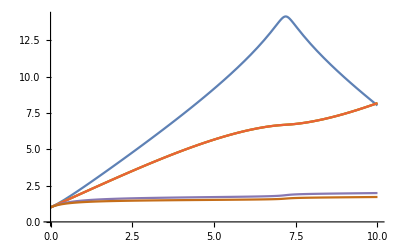

```mathematica
Plot[ Evaluate[ q /. solution[t]], { t, 0, 10 } ]
```

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{r[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}

r[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

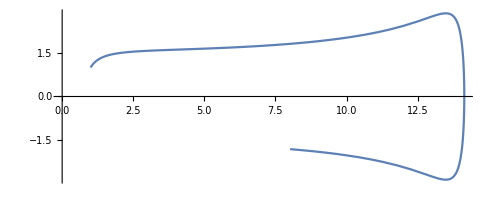

```mathematica
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, 10 } ]
```

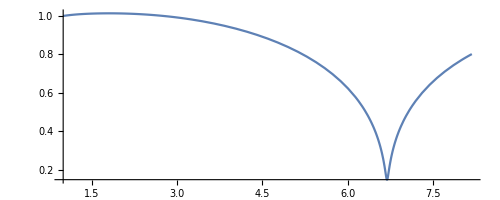

```mathematica
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, 10 } ]
```

```mathematica
ParametricPlot[ { solution[t][[3,2]] , solution'[t][[3,2]] } , { t , 0, 10 } ]
```

-Graphics-

```mathematica
ParametricPlot[ { solution[t][[4,2]] , solution'[t][[4,2]] } , { t , 0, 10 } ]
```

-Graphics-

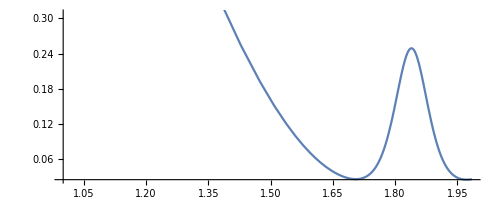

```mathematica
ParametricPlot[ { solution[t][[5,2]] , solution'[t][[5,2]] } , { t , 0, 10 } ]
```

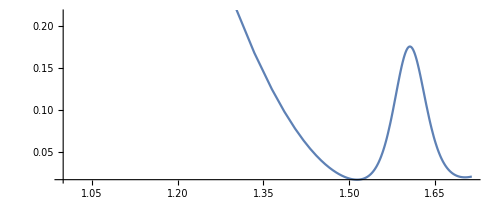

```mathematica
ParametricPlot[ { solution[t][[6,2]] , solution'[t][[6,2]] } , { t , 0, 10 } ]
```